```mathematica
ex1=Grid[{{
-Graphics-,
Spacer[1],
Style[
(*Column[{ 
Item[ButtonBar[{Graphics[{Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]},ImageSize->20]:>FrontEndTokenExecute[InputNotebook[],"SelectionOpenAllGroups"],Graphics[{Polygon[{{1,Sqrt[3]},{0,0},{-1,Sqrt[3]}}]},ImageSize->20]:>FrontEndTokenExecute[InputNotebook[],"SelectionCloseAllGroups"]
},Background->RGBColor[0.811765,0.721569,0.486275]],Alignment->Center],*)
Column[{
ActionMenu[Style[" Contents ",16],{
Style["Ideal Solutions",Bold,15]:>NotebookLocate["Ideal Solutions"],
Framed@Style["Pressure-Composition Diagrams (P-x-y)",Bold,14]:>NotebookLocate["Pressure-Composition Diagrams"],
Style["Raoult's Law",Bold,Italic,13]:>NotebookLocate["Raoult's Law"],
Row[{Style["Screencast:",Bold]," Raoult's Law"}]:>NotebookLocate["link 1"],
"💡 Derivation of Raoult's Law":>NotebookLocate["Derivation of Raoult's Law"],
Style["Mapping a P-x-y Diagram",Bold,Italic,13]:>NotebookLocate["Mapping a P-x-y Diagram"],
Style["Figure 1",Italic]:>NotebookLocate["Figure 1"],
Style["Lever Rule",Bold,Italic,13]:>NotebookLocate["Lever Rule"],
Row[{Style["Screencast:",Bold]," Lever Rule"}]:>NotebookLocate["link 2"],
Style["Figure 2",Italic]:>NotebookLocate["Figure 2"],
"Concept Test 1":>NotebookLocate["Concept Test 1"],
"💡 Solution 1":>NotebookLocate["Solution 1"],
Style["Figure 3",Italic]:>NotebookLocate["Figure 3"],
Style["Changes in Pressure",Bold,Italic,13]:>NotebookLocate["Changes in Pressure"],
"Effect on Liquid and Vapor Amounts (Lever Rule)":>NotebookLocate["Effect on Liquid and Vapor Amounts (Lever Rule)"],
Style["Figure 4",Italic]:>NotebookLocate["Figure 4"],
"Effect on Molar Composition in the Liquid and Vapor Phases":>NotebookLocate["Effect on Molar Composition in the Liquid and Vapor Phases"],
"Concept Test 2":>NotebookLocate["Concept Test 2"],
Style["Figure 5",Italic]:>NotebookLocate["Figure 5"],
Style["Figure 6",Italic]:>NotebookLocate["Figure 6"],
Row[{Style["Screencast:",Bold]," Add a Component to Binary system in VLE"}]:>NotebookLocate["link 3"],
"Concept Test 3":>NotebookLocate["Concept Test 3"],
Style["Figure 7",Italic]:>NotebookLocate["Figure 7"],
Style["Changes in Temperature",Bold,Italic,13]:>NotebookLocate["Changes in Temperature"],
"Exercise 1":>NotebookLocate["Exercise 1"],
Style["Figure 8",Italic]:>NotebookLocate["Figure 8"],
"Concept Test 4":>NotebookLocate["Concept Test 4"],
"💡 Solution 4":>NotebookLocate["Solution 4"],
Style["Figure 9",Italic]:>NotebookLocate["Figure 9"],
"Concept Test 5":>NotebookLocate["Concept Test 5"],
Style["Figure 10",Italic]:>NotebookLocate["Figure 10"],
"Concept Test 6":>NotebookLocate["Concept Test 6"],
Style["Figure 11",Italic]:>NotebookLocate["Figure 11"],
Framed@Style["Temperature-Composition Diagrams (T-x-y)",Bold,14]:>NotebookLocate["Temperature-Composition Diagrams"],
Style["Raoult's Law",Bold,Italic,13]:>NotebookLocate["Raoult's Law T-x-y"],
Style["Figure 12",Italic]:>NotebookLocate["Figure 12"],
Row[{Style["Screencast:",Bold]," Bubble Temperature: Raoult's Law"}]:>NotebookLocate["link 4"],
Style["Mapping a T-x-y Diagram",Bold,Italic,13]:>NotebookLocate["Mapping a T-x-y Diagram"],
Style["Figure 13",Italic]:>NotebookLocate["Figure 13"],
Style["Changes in Temperature",Bold,Italic,13]:>NotebookLocate["Changes in Temperature T-x-y"],
"Effect on Liquid and Vapor Amounts (Lever Rule)":>NotebookLocate["Effect on Liquid and Vapor Amounts (Lever Rule) T-x-y"],
Style["Figure 14",Italic]:>NotebookLocate["Figure 14"],
Row[{Style["Screencast:",Bold]," T-x-y Diagram: Lever Rule (Review)"}]:>NotebookLocate["link 5"],
"Effect on Molar Composition in the Liquid and Vapor Phases":>NotebookLocate["Effect on Molar Composition in the Liquid and Vapor Phases T-x-y"],
"Concept Test 7":>NotebookLocate["Concept Test 7"],
Style["Figure 15",Italic]:>NotebookLocate["Figure 15"],
Style["Figure 16",Italic]:>NotebookLocate["Figure 16"],
Row[{Style["Screencast:",Bold]," Phase Equilibrium: T-x-y Diagram"}]:>NotebookLocate["link 6"],
"Adding Energy to a System":>NotebookLocate["Adding Energy to a System"],
Style["Figure 17",Italic]:>NotebookLocate["Figure 17"],
Style["Changes in Pressure",Bold,Italic,13]:>NotebookLocate["Changes in Pressure T-x-y"],
"Concept Test 8":>NotebookLocate["Concept Test 8"],
Style["Figure 18",Italic]:>NotebookLocate["Figure 18"]
},Background->RGBColor[0.811765,0.721569,0.486275]]
(*},Alignment->Left]*),Text@Style["Baumann,  Falconer,  Maguire,  Nicodemus",White,Bold,13,FontFamily->"Arial"]}],
FontFamily->"Arial"]
}},ItemSize->{{38,20}}];

SetOptions[EvaluationNotebook[],{DockedCells->Cell[BoxData[ToBoxes[ex1]/.{(ImageSize->{___,___})->(ImageSize->{1399,10})}],"DockedCell",Background->Black,ImageMargins->0,CellMargins->{{0,0},{0,0}},CellFrameMargins->{{0,0},{0,0}}]}
];
```

# Vapor Liquid Equilibrium (VLE) for Ideal Solutions

## Pressure-Composition (P-x-y) Diagrams

The Gibbs phase rule is used to determine the number of degrees of freedom for a non-reactive system. F=C-P+2, where F is the number of degrees of freedom, C is the number of components, and P is the number of phases present. For a single pure component, F=1 so vapor-liquid equilibrium occurs only at the boiling point, but for a binary mixture F=2. For a system at a fixed temperature, both pressure and composition can be varied in the binary mixture to gather data to create a pressure-composition (P-x-y) diagram. This data forms the bubble-point and dew-point curves. Any system in between these two curves (including on the equilibrium curves) will form vapor-liquid equilibrium.

## Raoult’s Law

Raoult’s law is a model that relates the partial pressure of a component to its saturaton pressure and liquid composition.  It is used to calculate the bubble-point (BP) and dew-point (DP) curves of an ideal mixture in vapor-liquid equilibrium. Examples of ideal solutions include: benzene-toluene, pentane-hexane, and n-hexane-n-octane. The equations for these curves are shown below:

P_BP=P_x=x_1 P_1^sat+(1-x_1) P_2^sat

P_DP=P_y=1/(y_1/P_1^sat+(1-y_1)/P_2^sat)

For a more detailed explanation of Raoult’s law, please view this Screencast (Raoult’s Law Explanation).

### Derivation of Raoult’s Law:

(**Maybe make this an optional closed box - as in - state that they can open this to see a derivation but its not critical to have)

Raoult’s law states that for a binary mixture:

P=x_1 P_1^sat+x_2 P_2^sat

Equation (0.1) can be rewritten to eliminate the x_2 term.

P=x_1 P_1^sat+(1-x_1) P_2^sat

The Antoine equation is used to get the saturation pressures of each component (P_1^sat and P_2^sat).

log_10(P_i^sat)=A-B/(T+C)

In equation (0.3) A, B, and C are empirical constants specific to each component. The values can be found in tabulated data.

For the bubble-point (BP) calculation ∑y_i=∑K_i x_i=1 is used to find the BP pressure. K_i is called the K-ratio of component i; according to Raoult’s law, K_i is the ratio of the component partial pressure to the total pressure K_i=P_i^sat/P.

1=P_1^sat/P x_1+P_2^sat/P (1-x_1)

Multiplying equation (0.4) through by P will return equation (0.1).

For the dew-point (DP) calculation, ∑y_i/K_i=1 is used to calculate the DP pressure.

y_1 P/P_1^sat+(1-y_1) P/P_2^sat=1

Rearranging equation (0.5) to solve for pressure as a function of the molar composition in the vapor phase (of the more volatile component, 1) is the DP pressure.

P=1/(y_1/P_1^sat+(1-y_1)/P_2^sat)

## Mapping a P-x-y Diagram

The blue line represents the bubble-point equilibrium line. At higher pressures above this boundary, both components are in the liquid phase. The green line represents the dew-point equilibrium line. At lower pressures below this boundary both components are in the vapor phase. Inside the shaded region between the two curves is the 2-phase region. The amount of each phase that is present at a certain system composition in the 2-phase region is determined from the lever rule (Figure 1).

(** change dot legend to line legend)

```mathematica
Framed[Column[{
Manipulate[Module[{Px,Py},
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0,2.}},Frame->True,Background->White,PlotLabel->Style[Row[{Subsuperscript["P","1","sat"]," > "Subsuperscript["P","2","sat"]}],17,FontFamily->"Arial"],FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},ImageSize->500,Filling->{1->{{2},Opacity[0.1,Blend[{Blue,RGBColor[0.1,0.6,0]},0.5]]}},
Epilog->{
Inset[Text@Style["liquid",18,FontFamily->"Arial",Darker[Gray,0.4]],Scaled[{0.25,0.65}]],
Inset[Text@Style["vapor",18,FontFamily->"Arial",Darker[Gray,0.4]],Scaled[{0.8,0.1}]],
Inset[Text@Style["2-phase",18,FontFamily->"Arial",Darker[Gray,0.4]],{0.5,0.5*(Px[0.5]+Py[0.5])}],
Inset[Text@Style[Row[{Style["●",20,Blue]," bubble-point"}],16,FontFamily->"Arial"],Scaled[{0.35,0.9}]],
Inset[Text@Style[Row[{Style["●",20,RGBColor[0.1,0.6,0]]," dew-point"}],16,FontFamily->"Arial"],Scaled[{0.65,0.9}]]
}]],
Text@Style["saturation pressures (bar):",FontFamily->"Arial",13],
{{Psat1,1.75,"component 1"},1.65,2.5,0.05},
{{Psat2,0.3,"component 2"},0.1,0.4,0.01}],
Text@Style["Figure 1",16,Bold,FontFamily->"Arial",Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 1

## Lever Rule

The lever rule is used to determine the relative amounts of liquid and vapor in the system.

An explanation of the lever rule is shown in this Screencast (Lever Rule).

Liquid amount present at z:     f^L=(y-z)/(y-x)

Vapor amount present at z:      f^V=(x-z)/(x-y)

Mouseover Figure 2 to see what points are used in the lever rule calculation.

```mathematica
Framed[Column[{
Framed@Module[{p,Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
p=0.733;
Psat1=1.569; 
Psat2=0.319; 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.4<y1,(y1-0.4)/(y1-x1),
Px[0.4]≤p,1,
Py[0.4]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},Frame->True,PlotRange->{{0,1},{0.3,1.6}},FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{0.4,p}]];
p2=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{0.4,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.4,p},{y1,p}}]},
{Thickness[0.005],Line[{{x1,p},{x1,p+0.04},{0.39,p+0.04},{0.39,p}}]},{Thickness[0.005],Line[{{(x1+0.4)/2,p+0.04},{(x1+0.4)/2,p+0.4}}]},
{Thickness[0.005],Line[{{0.41,p},{0.41,p+0.04},{y1,p+0.04},{y1,p}}]},{Thickness[0.005],Line[{{(0.4+y1)/2,p+0.04},{(0.4+y1)/2,p+0.4}}]},
Text[Style[Column[{Row[{NumberForm[leverx*100,2],"%"}],"liquid"},Alignment->Center],17,FontFamily->"Arial"],{(y1+0.4)/2,p+0.5}],
Text[Style[Column[{Row[{NumberForm[levery*100,2],"%"}],"vapor"},Alignment->Center],17,FontFamily->"Arial"],{(x1+0.4)/2,p+0.5}]
}];
p3=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{0.4,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.4,p},{y1,p}}]},
{Thickness[0.005],Line[{{x1,p},{x1,p+0.04},{0.39,p+0.04},{0.39,p}}]},{Thickness[0.005],Line[{{(x1+0.4)/2,p+0.04},{(x1+0.4)/2,p+0.4}}]},
{Thickness[0.005],Line[{{0.41,p},{0.41,p+0.04},{y1,p+0.04},{y1,p}}]},{Thickness[0.005],Line[{{(0.4+y1)/2,p+0.04},{(0.4+y1)/2,p+0.4}}]},
Text[Style["L",17,FontFamily->"Arial"],{(y1+0.4)/2,p+0.45}],
Text[Style["V",17,FontFamily->"Arial"],{(x1+0.4)/2,p+0.45}],
{PointSize[0.015],Point[{x1,p}]},Text[Style["x_1",17,FontFamily->"Arial"],{x1,p},{-1,1}],
{PointSize[0.015],Point[{0.4,p}]},Text[Style["z_1",17,FontFamily->"Arial"],{0.415,p},{-1,1}],
{PointSize[0.015],Point[{y1,p}]},Text[Style["y_1",17,FontFamily->"Arial"],{y1,p},{-1,1}]
}];
Mouseover[Show[p1,p2,Background->White],Show[p1,p3,Background->White]]
],
Text@Style["Figure 2",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center]]
```

Figure 2

Practice Problem

Based on the ideal mixture in the P-x-y diagram (Figure 2) at the pressure shown, use the lever rule to calculate the amount of liquid and vapor present for an overall molar composition z_1=0.6. Note that the composition of component 1 in the liquid phase at constant pressure is x_1=0.33 and in the vapor phase, y_1=0.71.

#### Solution

The fraction of liquid present (f^L) is,

	f^L=L/(L+V)=(z_1-y_1)/(x_1-y_1)=(0.6-0.71)/(0.33-0.71)=0.29   or  29%   liquid
	
The fraction of vapor present (f^V) is,

	f^V=V/(L+V)=(z_1-x_1)/(y_1-x_1)=(0.6-0.33)/(0.71-0.33)=0.71   or  71%  vapor

Use the Demonstration below to see how the amount of liquid and vapor present changes with overall composition (Figure 3).

```mathematica
Framed[Column[{Manipulate[
Module[{p,Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
p=0.733;
Psat1=1.569; 
Psat2=0.319; 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<comp<y1,(y1-comp)/(y1-x1),
Px[comp]≤p,1,
Py[comp]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0.,1.75}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},AxesOrigin->{0,100},ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{comp,p}]];
p2=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{comp,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{comp,p},{y1,p}}]},
If[comp>0.33,{Thickness[0.0045],Line[{{x1,p},{x1,p+0.04},{comp-0.01,p+0.04},{comp-0.01,p}}]}],{Thickness[0.0045],Line[{{(x1+comp)/2,p+0.04},{(x1+comp)/2,p+0.4}}]},
If[comp<0.71,{Thickness[0.0045],Line[{{comp+0.01,p},{comp+0.01,p+0.04},{y1,p+0.04},{y1,p}}]}],{Thickness[0.0045],Line[{{(comp+y1)/2,p+0.04},{(comp+y1)/2,p+0.4}}]},
Text[Style[Column[{Row[{NumberForm[leverx*100,2],"%"}],"liquid"},Alignment->Center],17,FontFamily->"Arial",Background->White],{(y1+comp)/2,p+0.55}],
Text[Style[Column[{Row[{NumberForm[levery*100,2],"%"}],"vapor"},Alignment->Center],17,FontFamily->"Arial"],{(x1+comp)/2,p+0.55}]
}];
p3=Graphics[{
{Thickness[0.003425],Line[{{0.05+(y1+comp)/2,0.4},{(y1+comp)/2,p}}]},
Text[Framed[Style["f^L=L/(L + V)",17,FontFamily->"Arial"],Background->White],{(y1+comp)/2,0.3},{-1,0}],
{Thickness[0.003425],Line[{{-0.05+(x1+comp)/2,0.4},{(x1+comp)/2,p}}]},
Text[Framed[Style["f^V=V/(L + V)",17,FontFamily->"Arial"],Background->White],{(x1+comp)/2,0.3},{1,0}]
}];
Show[p1,p2,p3]],
{{comp,0.6,Style["overall molar composition (z_1)",13,FontFamily->"Arial"]},0.33,0.71,0.01,Appearance->"Labeled"}],
Text@Style["Figure 3",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 3

## Changes in Pressure

For an ideal mixture at a constant overall composition (z_1=0.5), observe how varying the system pressure affects the amount of liquid and vapor present, and the compositions in each phase.

### Effect on Liquid and Vapor Amounts (Lever Rule)

As the binary mixture is compressed, keeping overall composition constant, more liquid is formed that is enriched in the less volatile component (Figure 4).

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
Psat1=1.569;
Psat2=0.319;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0.3,1.6}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},ImageSize->{450,300},
Epilog->Inset[Graphics[{PointSize[0.09],Point[{0,0}]}],{0.5,p}]];
p2=BarChart[{leverx,levery},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,290},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverx,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*levery,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center]];
p3=Graphics[{
If[leverx==1∨levery==1,Text[""],
{{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,p},{y1,p}}]}}]
}];
Row[{Show[p1,p3],Show[p2]}]
],
{{p,0.707,Style["pressure (bar)",13,FontFamily->"Arial"]},0.25,1.25,0.05,Appearance->"Labeled"}],
Text@Style["Figure 4",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 4

### Effect on Molar Composition in the Liquid and Vapor Phases

Test Yourself

A piston-cylinder system (Figure 5) contains components A and B in vapor-liquid equilibrium (VLE). Assume the system is ideal, with x_A=0.25 and y_A=0.5. A small weight is added to the piston, while temperature is held constant. What happens to the system as pressure increases?

A. x_A increases, y_A decreases

Incorrect.

B. x_A increases, y_A increases

Correct. Use the slider in Figure 6 to increase the pressure and see x_A and y_A increase.

B. x_A increases, y_A increases

Correct. Use the slider in Figure 6 to increase the pressure and see x_A and y_A increase.

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,Px,Py,x0,y0,x1,y1,leverx,levery,p1,p2},
Psat1=1.569;
Psat2=0.319;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x0=X/.FindRoot[0.7==X*Psat1+(1-X)*Psat2,{X,0}];
y0=Y/.FindRoot[0.7==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0.1,1.6}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},ImageSize->400,
Epilog->Inset[Graphics[{PointSize[0.055],Point[{0,0}]}],{0.5,p}]];

p2=Graphics[{
{Thick,Dashed,Blend[{Blue,Gray},0.65],Line[{{x0,0.7},{0.5,0.7}}]},
{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.65],Line[{{0.5,0.7},{y0,0.7}}]},
{Thick,Dashed,Blend[{Blue,Gray},0.65],Line[{{x0,0.7},{x0,0.1}}]},
{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.65],Line[{{y0,0.7},{y0,0.1}}]},
{Gray,PointSize[0.02],Point[{0.5,0.7}]},

{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,p},{y1,p}}]},
{Thick,Dashed,Blue,Line[{{x1,p},{x1,0.133}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{y1,p},{y1,0.133}}]},
If[p==0.7,Text@"",{{Thick,Arrow[{{x0,0.2},{x1,0.2}}]},{Thick,Arrow[{{y0,0.2},{y1,0.2}}]}}]
}];
Show[p1,p2]
],{{p,0.7,"pressure (bar)"},0.55,0.9,0.01,Appearance->"Labeled"}],
Text@Style["Figure 6",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 6

C. x_A decreases, y_A decreases

Incorrect.

D. x_A decreases, y_A increases

Incorrect.

```mathematica
Framed@Column[{
Framed@Graphics3D[{
{Opacity[0.3],Cylinder[{{0,0,0},{0,0,2}},0.75]},
{Gray,Cylinder[{{0,0,1.5},{0,0,1.75}},0.75]},
{RGBColor[0.,0.65,0.9],Cylinder[{{0,0,0},{0,0,0.55}},0.75]},
{FaceForm[Black],Cuboid[{-0.25,0,2.25},{0.25,0,2.65}]},
{Thickness[0.02],Arrowheads[0.05],Arrow[{{0,0,2.25},{0,0,1.85}}]},
Text[Style[Column[{"vapor","y_A = 0.5"},Alignment->Center],18,FontFamily->"Arial"],{0,0,1.}],
Text[Style[Column[{"liquid","x_A = 0.25"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.15}]
},Boxed->False,ViewPoint->Front,Lighting->{{"Ambient",LightGray}},Background->White,ImageSize->150],
Text@Style["Figure 5",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center]
```

-Graphics3D-
Figure 5

For a complete explanation, view these Screencasts: Increase Pressure on Binary VLE System (Interactive) and Pressure Effect on VLE

Test Yourself

A 50/50 mol% liquid mixture of n-pentane and n-heptane is at high pressure (1.2 bar). The pressure is lowered isothermally until the mixture begins to vaporize (0.94 bar). The system behaves ideally and P_P^sat>P_H^sat. Which of the following statements is true (Figure 7)?

A. n-Heptane is enriched in the vapor phase

Incorrect.

B. n-Pentane is enriched in the vapor phase

Correct. n-Pentane is the more volatile component so it will be enriched in the vapor phase.

C. The composition in the vapor phase is 50/50 mol%

Incorrect.

D. The mixture does not vaporize

Incorrect.

```mathematica
Framed[Column[{
Manipulate[
Module[{Psat1,Psat2,Px,Py,x1,y1,leverL,leverV},
Psat1=1.569;
Psat2=0.319;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=x/.FindRoot[x*Psat1+(1-x)*Psat2==P,{x,0.4}];
y1=x/.FindRoot[(x/Psat1+(1-x)/Psat2)^-1==P,{x,0.5}];
leverL=If[P<Px[0.5],(0.5-y1)/(x1-y1),1];
leverV=1-leverL;
Show[Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Frame->True,FrameLabel->{Style["mole fraction of n-pentane",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},PlotRange->{{0,1},{0.1,1.6}},
LabelStyle->FontSize->16,ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.045],Point[{0,0}]}],{0.5,P}]],
If[P<Px[0.5],
Graphics[{
{Thick,Blue,Dashed,Line[{{x1,P},{0.5,P}}]},
{Thick,Blue,Dashed,Line[{{x1,P},{x1,0.1}}]},
{Thick,RGBColor[0.1,0.6,0],Dashed,Line[{{0.5,P},{y1,P}}]},
{Thick,RGBColor[0.1,0.6,0],Dashed,Line[{{y1,P},{y1,0.1}}]},
Text[Framed[Style[Row[{"x = ",NumberForm[x1,2]}],17,FontFamily->"Arial"],Background->LightGray],{x1,0.65*P}],
Text[Framed[Style[Row[{"y = ",NumberForm[y1,2]}],17,FontFamily->"Arial"],Background->LightGray],{y1,0.65*P}],

{Thickness[0.0035],Line[{{0.5*(x1+0.5)-0.05,1},{0.5*(x1+0.5),P}}]},
{Thickness[0.0035],Line[{{0.5*(y1+0.5)+0.05,1},{0.5*(y1+0.5),P}}]},
Text[Framed[Style[Row[{NumberForm[100*leverL,2],"% L"}],17,FontFamily->"Arial"],Background->LightGray],{0.5*(y1+0.5)+0.05,1}],
Text[Framed[Style[Row[{NumberForm[100*leverV,2],"% V"}],17,FontFamily->"Arial"],Background->LightGray],{0.5*(x1+0.5)-0.05,1}]
}],
Graphics[{
{Thickness[0.0035],Line[{{0.35,1.4},{0.5,P}}]},
Text[Framed[Style["50/50 mol%",17,FontFamily->"Arial"],Background->LightGray],{0.35,1.4}]
}]
]]
],
{{P,1.2,Style["drop pressure after answering concept test",13,FontFamily->"Arial"]},1.2,0.7,Trigger,AnimationRate->10,AppearanceElements->{"PlayPauseButton","ResetButton"}}],
Text@Style["Figure 7",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 7

## Changes in Temperature

### Exercise

Hypothesize how increasing the temperature will affect the equilibrium curves on a P-x-y diagram (Figure 8)?

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,T0,Px0,Py0,Px,Py,p0,p1},
Psat1=0.00133322368*10^(6.90565-1211.033/(T+220.79)); 
Psat2=0.00133322368*10^(6.65464-1344.8/(T+219.48)); 
T0=105;
Px0[x_]=x*0.00133322368*10^(6.90565-1211.033/(T0+220.79))+(1-x)*0.00133322368*10^(6.65464-1344.8/(T0+219.48));
Py0[x_]=(x/(0.00133322368*10^(6.90565-1211.033/(T0+220.79)))+(1-x)/(0.00133322368*10^(6.65464-1344.8/(T0+219.48))))^-1;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
Plot[{Px[x],Py[x],Px0[x],Py0[x]},{x,0,1},
PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]},{Thick,Dashed,Blend[{Blue,Gray},0.5]},{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.5]}},
PlotRange->{{0,1},{0.1,3}},Frame->True,
FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},LabelStyle->FontSize->16,ImageSize->500]
],
{{T,105,Style["temperature (°C)",13,FontFamily->"Arial"]},90,120,5,Appearance->"Labeled"}],
Text@Style["Figure 8",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 8

Test Yourself

For a 50/50 mixture of two ideal components in VLE at 0.75 bar, will the amount of liquid in the system increase or decrease if the temperature is raised (Figure 9)? (Bonus: Will it be more drastic or less drastic a change at higher pressures?)

#### Solution

The amount of liquid present will decrease, subsequently the amount of vapor increases. Move the temperature slider to see how the amount of liquid and vapor phases change. A different pressure can also be chosen (Figure 9).

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
Psat1=0.00133322368*10^(6.90565-1211.033/(T+220.79)); 
Psat2=0.00133322368*10^(6.65464-1344.8/(T+219.48)); 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},PlotRange->{{0,1},{0.1,3}},LabelStyle->{Black,FontFamily->"Arial"},LabelStyle->FontSize->16,ImageSize->{450,300},
Epilog->Inset[Graphics[{PointSize[0.085],Point[{0,0}]}],{0.5,p}]
];
p2=BarChart[{leverx,levery},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,290},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverx,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*levery,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center]];
p3=Graphics[{
If[leverx==1∨levery==1,Text[""],
{{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,p},{y1,p}}]}}]
}];
Row[{Show[p1,p3],Show[p2]}]
],
{{T,95,Style["temperature (°C)",13,FontFamily->"Arial"]},90,120,5,Appearance->"Labeled"},
{{p,0.75,Style["pressure (bar)",13,FontFamily->"Arial"]},{0.55,0.75,0.95,1.15}}],
Text@Style["Figure 9",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 9

Test Yourself

We want to separate 50/50 mixtures of benzene and toluene in the vapor phase. As temperature is lowered, the technician observes that toluene condenses before benzene. Is this possible?

Hint

Consider Raoult’s law

A. Yes, if benzene has a lower vapor pressure than toluene.

Incorrect.

B. Yes, if benzene has a higher vapor pressure than toluene.

Incorrect.

C. No, both species have to condense.

Correct. Since these two components are miscible, both will condense (Figure 10).

```mathematica
Framed[Column[{Manipulate[
Module[{T1,Psat1,Psat2,Px,Py,T,Psat1i,Psat2i,P1,P2,P},
Psat1=2.05747;
Psat2=0.431584;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
T=120-Tp+80;
Psat1i=0.001333222368*10^(6.90565-1211.033/(T+220.79)); 
Psat2i=0.00133322368*10^(6.65464-1344.8/(T+219.48)); 
P1=p/.FindRoot[p==0.5*Psat1i+(1-0.5)*Psat2i,{p,0.2}];
P2=p/.FindRoot[p==1/(0.5/Psat1i+(1-0.5)/1Psat2i),{p,0.2}];
P=0.5*(P1+P2);
Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Frame->True,FrameLabel->{Style["mole fraction of benzene",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},LabelStyle->FontSize->16,ImageSize->400,
Epilog->{
Inset[Graphics[{PointSize[0.04],Point[{0,0}]}],{0.5,P}],
Inset[Graphics[Text@Style["liquid",16,FontFamily->"Arial"]],{0.15,1.5}],
Inset[Graphics[Text@Style["vapor",16,FontFamily->"Arial"]],{0.75,0.65}]
}
]
],
{{Tp,95,Style["temperature (°C)",13,FontFamily->"Arial"]},90,150,5,Appearance->"Labeled"}],
Text@Style["Figure 10",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 10

D. It depends on the system pressure as to whether one or two species condense.

(**->??)	Incorrect.

Test Yourself

For the starting conditions shown in Figure 11, 2 moles octane are added to 20.1 moles hexane in vapor-liquid equilibrium (P_O^sat<P_H^sat). The system can be modeled by Raoult’s law. What happens to the components in the system? Move your mouse over the figure to view the P-x-y diagram. Once you have solved the problem, click “inject isothermally” to observe the change.

A. All condense

Correct. Since only hexane in VLE was present, the addition of octane (less volatile) will result in all components condensing (see Figure 11).

B. All vaporize

Incorrect.

C. A vapor-liquid mixture forms

Incorrect.

```mathematica
Framed[Column[{Manipulate[
Module[{nL,nV,nTo,nT,zH,zi,P,Psati,PsatH,PsatO,ρHL,ρHV,vL,vV,amtL,amtV,step,Δ1,Δ2,tank,piston,amounts,labels,Psat1,Psat2,plotPxy},
nL=20;
nV=0.1;
nTo=20.1;
nT=nTo+2;
zH=nTo/nT;
zi=2/nT;
P=zH*PsatH+(1-zH)*PsatO;
Psati=If[cs==1,PsatO,PsatH];
PsatH=0.247474;
PsatO=0.024569;
ρHL=0.6548;
ρHV=3.64*^-4;
vL=2*((nL*86.18)/ρHL+If[cs==1,1/ρHL(2+0.1)*86.18*(1-step),-(nL*86.18)/ρHL*(1-step)]);
vV=(nV*86.18)/ρHV+If[cs==2,((2+0.1)*86.18)/ρHV*(1-step),0];
amtL=vL/(vL+vV);
amtV=vV/(vL+vV);
step=If[cs==1,(amt-1)/0.75,(amt2-1)/0.75];
Δ1=2.75*(zi-nV);
Δ2=2.25-2.75*amtL;
tank=Graphics3D[{
{Opacity[0.5],Cylinder[{{0,0,0},{0,0,2.75}}]},
{Opacity[0.75],RGBColor[0.066667,1,0.593469],Cylinder[{{0,0,0},{0,0,amtL*2.75}}]},
{Opacity[0.5],White,Cylinder[{{1,0,1.375},{2,0,1.375}},0.12]},
{Opacity[0.75],RGBColor[0.066667,1,0.593469],Cylinder[{{1,0,1.375},{1+(2*86.18)/(666*ρHL)*step,0,1.375}},0.12]},
{White,Cylinder[{{1+(2*86.18)/(666*ρHL)*step,0,1.375},{2+(2*86.18)/(666*ρHL)*step,0,1.375}},0.03]},
{Black,Cylinder[{{2+(2*86.18)/(666*ρHL)*step,0,1.375},{2.025+(2*86.18)/(666*ρHL)*step,0,1.375}},0.14]},
Text[Style[
If[ cs==1,
If[amt==1,
Row[{2," mol octane added"}],
Row[{"add ",2," mol octane"}]
],
If[amt2==1,
Row[{2," mol hexane added"}],
Row[{"add ",2," mol hexane"}]
]
],18,FontFamily->"Arial"],{2,0,1}],
{Gray,Cylinder[{{0,0,If[cs==1,2.25-Δ2*(1-step),2.25+0.5*(1-step)]},{0,0,If[cs==1,2.5-Δ2*(1-step),2.5+0.5*(1-step)]}}]},
{Gray,Cylinder[{{0,0,If[cs==1,2.25-Δ2*(1-step),2.25+0.5*(1-step)]},{0,0,3.5}},0.12]}
},Lighting->{{"Ambient",LightGray}},Boxed->False,ViewPoint->Front,PlotRange->{{-1,3.25},{-1,1},{0,3}}];

amounts=If[cs==1,
If[amt==1,
Graphics3D[{
Text[Style[Row[{2," mol octane"}],18,FontFamily->"Arial"],{0,0,0.55*2.75*amtL}],
Text[Style[Row[{nTo," mol hexane"}],18,FontFamily->"Arial"],{0,0,0.15*2.75*amtL}]
}],
Graphics3D[{
Text[Style[Row[{nL," mol liquid hexane"}],18,FontFamily->"Arial"],{0,0,0.15*2.75*amtL}],
Text[Style[Row[{nV," mol vapor hexane"}],18,FontFamily->"Arial"],{0,0,0.5*(2.25-(1-step)*Δ2+(2.75*nV+(1-step)*Δ1))}]
}]
],
If[amt2==1,
Graphics3D[Text[Column[{Style["all vapor",18,FontFamily->"Arial"],Style["*note: volumne not to scale*",14]},Alignment->Center],{0,0,2.75*0.5}]],
Graphics3D[{
Text[Style[Row[{nL," mol liquid octane"}],18,FontFamily->"Arial"],{0,0,0.15*2.75*amtL*(1+(1-step))}],
Text[Style[Row[{nV," mol vapor octane"}],18,FontFamily->"Arial"],{0,0,0.5*2.75}]
}]
]
];
labels=Graphics3D[
Text[Style[
If[cs==1,
If[amt==1,"all vapor condenses",""],
If[amt2==1,"all liquid evaporates",""]
],18,FontFamily->"Arial"],{2,0,1.75}]
];
plotPxy=Plot[{x*PsatH+(1-x)*PsatO,(x/PsatH+(1-x)/PsatO)^-1},{x,0,1},
Frame->True,
FrameLabel->{Style["hexane mole fraction",16],Style["pressure (bar)",16]},
LabelStyle->{Black,FontFamily->"Arial"},
PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
PlotRangeClipping->False,
ImagePadding->{{50,40},{52,5}},
Epilog->{
Inset[Style[Text@"pure octane",16,FontFamily->"Arial"],{0,-0.05}],
Inset[Style[Text@"pure hexane",16,FontFamily->"Arial"],{1,-0.05}],
If[cs==1,{
Inset[Style[If[amt<1.75,Text@"all liquid",Text@" "],18,FontFamily->"Arial"],{0.3,0.15}],
Inset[Graphics[{Disk[]},ImageSize->12],{1-zi*(1-step),PsatH}]
},
{
Inset[Style[If[amt2<1.75,Text@"all vapor",Text@" "],18,FontFamily->"Arial"],{0.75,0.025}],
Inset[Graphics[{Disk[]},ImageSize->12],{zi*(1-step),PsatO}]
}]
}
];
Mouseover[
Show[tank,amounts,labels,ImageSize->{420,320}],
Show[plotPxy,If[cs==1,
Graphics[{Thick,Dashed,Line[{{1-zi*(1-step),PsatH},{1,PsatH}}]}],
Graphics[{Thick,Dashed,Line[{{0,PsatO},{zi*(1-step),PsatO}}]}]
],ImageSize->{420,320}
]
]
],
Column[{
Control[{{cs,1,"component to inject"},{1->"octane",2->"hexane"},SetterBar}],
PaneSelector[{
1->Control[{{amt,1.75,"inject isothermally"},1.75,1,0.01,Trigger,AnimationRate->1,AppearanceElements->{"PlayPauseButton","ResetButton"}}],
2->Control[{{amt2,1.75,"inject isothermally"},1.75,1,0.01,Trigger,AnimationRate->1,AppearanceElements->{"PlayPauseButton","ResetButton"}}]
},Dynamic@cs]
}]
],Text@Style["Figure 11",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 11

In the question above, the less volatile component (octane) is added. Predict what happens if hexane is added to octane in VLE. Will all the components condense? Vaporize? Or form a VLE mixture? In Figure 11, select “add hexane” to see what happens.

## Temperature-Composition (T-x-y) Diagrams

## Raoult’s Law

Raoult’s law is used to calculate the dew-point and bubble-point of a binary mixture just like how it is used when looking at a P-x-y diagram.  However, the bubble- and dew-temperatures have to be solved for iteratively due to the temperature dependence of the vapor pressures.

For a known liquid composition (x_i) and pressure, the vapor composition (y_i) and temperature can be calculated using a guess-and-check method. Recall the K-ratio for an ideal solution: K_i=P_i^sat/P.

Given x_1=0.6 and P=0.7 bar for a VLE mixture of benzene(1) and toluene(2), guess a value for T and calculate the saturation pressures.

T_(guess,1)=75 °C

	Log(P_1^sat)=9.28-2790/(T+221)=9.28-2790/(75+221)≈0.7 bar

	Log(P_2^sat)=9.39-3096/(T+219)=9.39-3096/(75+219)≈0.07 bar

Next calculate the K-ratios for this temperature.

K_1=P_1^sat/P=(0.7 bar)/(0.7 bar)≈1

	K_2=P_2^sat/P=(0.07bar)/(0.7 bar)≈0.1

For a bubble-point calculation ∑y_i=∑K_i x_i=1

y_1=K_1 x_1=(1)*0.6≈0.6

	y_2=K_2 x_2=(0.1)*(1-0.6)≈0.04

	∑y_i=0.6+0.04=0.64<1

Since the sum does not add up to 1, a higher guess is needed. Typically these iterative calculations are done using data analysis software.  It can also be performed in Mathematica as shown here:

Module[{P, Psat1, Psat2, x},
 P = 0.7;
 Psat1[T_] = 10^(9.2806 - 2789.51/(T + 220.64));
 Psat2[T_] = 10^(9.3935 - 3096.52/(T + 219.33));
 x = 0.6;
 T /. FindRoot[x*Psat1[T] + (1 - x)*Psat2[T] == P, {T, 70}]]

81.0909

In Figure 12 the first guess (75°C) is shown below the saturation curve and the correct temperature (81°C) is shown on it.

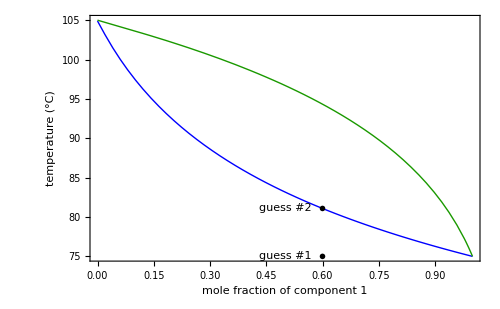
-Graphics-
Figure 12

```mathematica
Framed@Column[{Framed@Module[{Pe,Psat1e,Psat2e,i,Txtable,Tytable,Txx,Tyy},
Pe=0.7;
Psat1e[Te_]=10^(9.2806-2789.51/(Te+220.64));
Psat2e[Te_]=10^(9.3935-3096.52/(Te+219.33));
i=0;
While[i<101,{xe=0.01*i,
s=FindRoot[xe*Psat1e[Te]+(1-xe)*Psat2e[Te]==Pe,{Te,90,150}];
xeq[i]=xe,
yeq[i]=(Psat1e[Te]*xe)/Pe/.s,
Teq[i]=Te/.s,i++}];
Txtable=Table[{xeq[i],Teq[i]},{i,1,100}];
Tytable=Table[{yeq[i],Teq[i]},{i,1,100}];
Txx=Interpolation[Txtable,InterpolationOrder->1];
Tyy=Interpolation[Tytable,InterpolationOrder->1];

Quiet@Plot[{Txx[x],Tyy[x]},{x,0,1},
ImageSize->500,Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Epilog->{
Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{0.6,81.0909}],
Inset[Text@Style["guess #1",FontFamily->"Arial",16],{0.5,75}],
Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{0.6,75}],
Inset[Text@Style["guess #2",FontFamily->"Arial",16,Background->White],{0.5,81.0909}]
}]],Text@Style["Figure 12",16,Bold,FontFamily->"Arial",Darker[Cyan,0.65]]},Alignment->Center]
```

In order to see how an entire T-x-y diagram can be plotted using the above method open the Mathematica code below.

Module[{P,Psat1,Psat2,i,Tx,Ty},
P=0.7;
Psat1[T_]=10^(9.2806-2789.51/(T+220.64));
Psat2[T_]=10^(9.3935-3096.52/(T+219.33));
i=0;
While[i<101,{xe=0.01*i,
s=FindRoot[xe*Psat1[T]+(1-xe)*Psat2[T]==P,{T,90,150}];
xeq[i]=xe,
yeq[i]=(Psat1[T]*xe/P)/.s,
Teq[i]=T/.s,i++}];
Tx=Interpolation[Table[{xeq[i],Teq[i]},{i,1,100}],InterpolationOrder→1];
Ty=Interpolation[Table[{yeq[i],Teq[i]},{i,1,100}],InterpolationOrder→1];
Plot[{Tx[x],Ty[x]},{x,0,1}]]

To see another example of solving for the bubble temperature, view this Screencast: Bubble Temperature: Raoult’s Law

## Mapping a T-x-y Diagram

The T-x-y diagram in Figure 13 is at constant pressure. At the bubble-point, the mixture will begin to vaporize. Further increases in temperature increases the amount of vapor until the point beyond the dew-point line, where the entire mixture is in the vapor phase.  The opposite is true starting with all vapor and decreasing the temperature.  The equilibrum lines and the shaded region represents the 2-phase region.

(**CHange legend to lines)

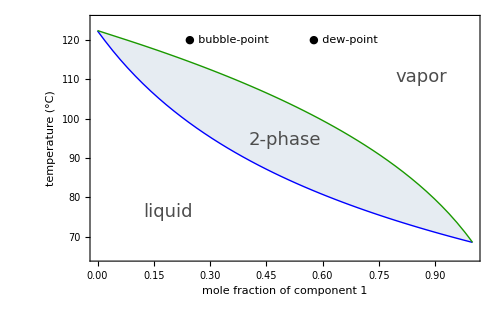
-Graphics-
Figure 13

```mathematica
Framed@Column[{Framed@Module[{Pe,Psat1e,Psat2e,i,Txtable,Tytable,Txx,Tyy},
Pe=0.7;
Psat1e[Te_]=0.00133322368*10^(6.90565-1211.033/(Te+220.79)); 
Psat2e[Te_]=0.00133322368*10^(6.65464-1344.8/(Te+219.48));  
i=0;
While[i<101,{xe=0.01*i,
s=FindRoot[xe*Psat1e[Te]+(1-xe)*Psat2e[Te]==Pe,{Te,40,190}];
xeq[i]=xe,
yeq[i]=(Psat1e[Te]*xe)/Pe/.s,
Teq[i]=Te/.s,i++}];
Txtable=Table[{xeq[i],Teq[i]},{i,1,100}];
Tytable=Table[{yeq[i],Teq[i]},{i,1,100}];
Txx=Interpolation[Txtable,InterpolationOrder->1];
Tyy=Interpolation[Tytable,InterpolationOrder->1];

Quiet@Plot[{Txx[x],Tyy[x]},{x,0,1},
PlotRange->{{0,1},{65,125}},ImageSize->500,Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Filling->{1->{{2},Opacity[0.1,Blend[{Blue,RGBColor[0.1,0.6,0]},0.5]]}},
Epilog->{
Inset[Row[{Style["●",20,Blue],Style[" bubble-point",16,FontFamily->"Arial"]}],Scaled[{0.35,0.9}]],
Inset[Row[{Style["●",20,RGBColor[0.1,0.6,0]],Style[" dew-point",16,FontFamily->"Arial"]}],Scaled[{0.65,0.9}]],
Inset[Style["liquid",18,Darker[Gray,0.4],FontFamily->"Arial"],Scaled[{0.2,0.2}]],
Inset[Style["vapor",18,Darker[Gray,0.4],FontFamily->"Arial"],Scaled[{0.85,0.75}]],
Inset[Style["2-phase",18,Darker[Gray,0.4],FontFamily->"Arial"],{0.5,0.5*(Txx[0.5]+Tyy[0.5])}]
}]],Text@Style["Figure 13",16,Bold,FontFamily->"Arial",Darker[Cyan,0.65]]},Alignment->Center]
```

## Changes in Temperature

For an ideal mixture at constant overall composition (z=0.5) use the demonstrations below to see how varying temperature affects the amounts of liquid and vapor present and the compositions in each phase.

### Effect on Liquid and Vapor Amounts (Lever Rule)

As temperature is increased, more of the mixture vaporizes in the two phase region (Figure 14). Recall from the previous section on P-x-y diagrams, if the pressure is raised the mixture is compressed and condenses. It is important to understand the reverse relationship between pressure and temperature effects.

```mathematica
Framed[Column[{Manipulate[Module[{Tx,Ty,x1,y1,leverL,leverV,p1,p2,p3},
Tx=Interpolation[{{0.05,116.17593775316534},{0.1,110.89064288898308},{0.15000000000000002,106.28016426869732},{0.2,102.20948552122492},{0.25,98.57815974289365},{0.30000000000000004,95.30990723431995},{0.35000000000000003,92.34572393006421},{0.4,89.63921049336349},{0.45,87.15333748547953},{0.5,84.85815968745945},{0.55,82.72917092945056},{0.6000000000000001,80.74609966165225},{0.65,78.89201335805389},{0.7000000000000001,77.15264298968454},{0.75,75.51586677076592},{0.8,73.97131084335041},{0.8500000000000001,72.51003696546866},{0.9,71.12429573098638},{0.9500000000000001,69.80732971380557},{1.,68.55321505054492}}];
Ty=Interpolation[{{0.19520547470774982,116.17593775316534},{0.3421787686820334,110.89064288898308},{0.4559066075854116,106.28016426869732},{0.5459474339199167,102.20948552122492},{0.6186280724359985,98.57815974289365},{0.6782730999826126,95.30990723431995},{0.7279222867367744,92.34572393006421},{0.7697651621557392,89.63921049336349},{0.8054130860444707,87.15333748547953},{0.8360746698514914,84.85815968745945},{0.8626718897371343,82.72917092945056},{0.8859187711815474,80.74609966165225},{0.9063758492293178,78.89201335805389},{0.9244885885770282,77.15264298968454},{0.940614960755704,75.51586677076592},{0.9550455524788249,73.97131084335041},{0.9680184401823779,72.51003696546866},{0.9797303388255023,71.12429573098638},{0.9903450598913365,69.80732971380557},{1.0000000000000009,68.55321505054492}}];
x1=Quiet[x/.FindRoot[Tx[x]==t,{x,0.1}]];
y1=Quiet[x/.FindRoot[Ty[x]==t,{x,0.1}]];
leverL=Which[t≤Tx[0.5],1,Tx[0.5]<t<Ty[0.5],(y1-0.5)/(y1-x1),t≥Ty[0.5],0];
leverV=1-leverL;
p1=Quiet@Plot[{Tx[x],Ty[x]},{x,0,1},
PlotRange->{{0,1},{65,125}},ImageSize->{450,300},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Epilog->Inset[Graphics[{PointSize[Large],Point[{0,0}]}],{0.5,t}]];
p2=BarChart[{leverL,leverV},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,290},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverL,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*leverV,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center]];
p3=Graphics[
If[leverL==1∨leverV==1,Text@"",
{{Thick,Dashed,Blue,Line[{{x1,t},{0.5,t}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,t},{y1,t}}]}}]
];
Row[{Show[p1,p3],Show[p2]}]
],{{t,95,"temperature (°C)"},75,115,5,Appearance->"Labeled"}],
Text@Style["Figure 14",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 14

For additional information on the lever rule and T-x-y diagrams, view this Screencast: T-x-y Diagram: Lever Rule (Review)

### Effect on Molar Composition in the Liquid and Vapor Phases

Test Yourself

A 50/50 mixture of A and B is heated under constant pressure. What happens to the liquid (x_A) and vapor (y_A) mole fractions as temperature is increased (Figure 15)? Recall what happens to x_A and y_A as pressure is increased (** Put this in a hint or in the answer - not in the question).

A. x_A increases, y_A increases

Incorrect.

B. x_A increases, y_A decreases

Incorrect.

C. x_A decreases, y_A increases

Incorrect.

D. x_A decreases, y_A decreases

Correct. Use the slider in Figure 16 to increase the temperature.

```mathematica
Framed[Column[{Manipulate[Module[{Tx,Ty,x0,y0,x1,y1,leverL,leverV,p1,p2},
Tx=Interpolation[{{0.05,116.17593775316534},{0.1,110.89064288898308},{0.15000000000000002,106.28016426869732},{0.2,102.20948552122492},{0.25,98.57815974289365},{0.30000000000000004,95.30990723431995},{0.35000000000000003,92.34572393006421},{0.4,89.63921049336349},{0.45,87.15333748547953},{0.5,84.85815968745945},{0.55,82.72917092945056},{0.6000000000000001,80.74609966165225},{0.65,78.89201335805389},{0.7000000000000001,77.15264298968454},{0.75,75.51586677076592},{0.8,73.97131084335041},{0.8500000000000001,72.51003696546866},{0.9,71.12429573098638},{0.9500000000000001,69.80732971380557},{1.,68.55321505054492}}];
Ty=Interpolation[{{0.19520547470774982,116.17593775316534},{0.3421787686820334,110.89064288898308},{0.4559066075854116,106.28016426869732},{0.5459474339199167,102.20948552122492},{0.6186280724359985,98.57815974289365},{0.6782730999826126,95.30990723431995},{0.7279222867367744,92.34572393006421},{0.7697651621557392,89.63921049336349},{0.8054130860444707,87.15333748547953},{0.8360746698514914,84.85815968745945},{0.8626718897371343,82.72917092945056},{0.8859187711815474,80.74609966165225},{0.9063758492293178,78.89201335805389},{0.9244885885770282,77.15264298968454},{0.940614960755704,75.51586677076592},{0.9550455524788249,73.97131084335041},{0.9680184401823779,72.51003696546866},{0.9797303388255023,71.12429573098638},{0.9903450598913365,69.80732971380557},{1.0000000000000009,68.55321505054492}}];
x0=0.305011;
y0=0.683658;
x1=Quiet[x/.FindRoot[Tx[x]==t,{x,0.1}]];
y1=Quiet[x/.FindRoot[Ty[x]==t,{x,0.1}]];
leverL=Which[t≤Tx[0.5],1,Tx[0.5]<t<Ty[0.5],(y1-0.5)/(y1-x1),t≥Ty[0.5],0];
leverV=1-leverL;
p1=Quiet@Plot[{Tx[x],Ty[x]},{x,0,1},
PlotRange->{{0,1},{65,125}},ImageSize->400,Frame->True,FrameLabel->{Style["mole fraction of component A",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Epilog->Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{0.5,t}]];
p2=Graphics[{
{Thick,Dashed,Blend[{Blue,Gray},0.65],Line[{{x0,65},{x0,95},{0.5,95}}]},
{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.65],Line[{{0.5,95},{y0,95},{y0,0.65}}]},
{Gray,PointSize[0.02],Point[{0.5,95}]},
{Thick,Dashed,Blue,Line[{{x1,65},{x1,t},{0.5,t}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,t},{y1,t},{y1,65}}]},
If[t==95,Text@"",{{Thick,Arrow[{{x0,70},{x1,70}}]},{Thick,Arrow[{{y0,70},{y1,70}}]}}]
}];
Show[p1,p2]
],{{t,95,"temperature (°C)"},85,104,1,Appearance->"Labeled"}],
Text@Style["Figure 16",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 16

```mathematica
Framed@Column[{
Framed@Graphics3D[{
{Opacity[0.3],Cylinder[{{0,0,0},{0,0,2}},0.75]},
{Gray,Cylinder[{{0,0,1.65},{0,0,1.85}},0.75]},
{RGBColor[0.,0.65,0.9],Cylinder[{{0,0,0},{0,0,0.55}},0.75]},
{FaceForm[Black],Cuboid[{-0.25,0,1.85},{0.25,0,2.25}]},
Text[Style[Column[{"vapor","y_A = 0.68"},Alignment->Center],18,FontFamily->"Arial"],{0,0,1.}],
Text[Style[Column[{"liquid","x_A = 0.31"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.15}]
},Boxed->False,ViewPoint->Front,Lighting->{{"Ambient",LightGray}},Background->White,ImageSize->150],
Text@Style["Figure 15",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center]
```

-Graphics3D-
Figure 15

For a complete explanation please view this Screencast: Phase Equilibrium: T-x-y Diagram

### Adding Energy to a System

As heat is added to the system, the temperature rises and the solution may vaporize depending on its location in the phase diagram. In Figure 17, a 50/50 mixture of two components is in vapor-liquid equilibrium at constant pressure. Use the slider to add heat to the system and see how this affects the amount of liquid and vapor in the system (lever rule). What happens as you add heat in each region and at eaach equilibrium line?

```mathematica
Framed[Column[{Quiet@Manipulate[Module[{Tx,Ty,x1,y1,leverL,leverV,T,p1,p2,p3},
Tx=Interpolation[{{0.05,116.17593775316534},{0.1,110.89064288898308},{0.15000000000000002,106.28016426869732},{0.2,102.20948552122492},{0.25,98.57815974289365},{0.30000000000000004,95.30990723431995},{0.35000000000000003,92.34572393006421},{0.4,89.63921049336349},{0.45,87.15333748547953},{0.5,84.85815968745945},{0.55,82.72917092945056},{0.6000000000000001,80.74609966165225},{0.65,78.89201335805389},{0.7000000000000001,77.15264298968454},{0.75,75.51586677076592},{0.8,73.97131084335041},{0.8500000000000001,72.51003696546866},{0.9,71.12429573098638},{0.9500000000000001,69.80732971380557},{1.,68.55321505054492}}];
Ty=Interpolation[{{0.19520547470774982,116.17593775316534},{0.3421787686820334,110.89064288898308},{0.4559066075854116,106.28016426869732},{0.5459474339199167,102.20948552122492},{0.6186280724359985,98.57815974289365},{0.6782730999826126,95.30990723431995},{0.7279222867367744,92.34572393006421},{0.7697651621557392,89.63921049336349},{0.8054130860444707,87.15333748547953},{0.8360746698514914,84.85815968745945},{0.8626718897371343,82.72917092945056},{0.8859187711815474,80.74609966165225},{0.9063758492293178,78.89201335805389},{0.9244885885770282,77.15264298968454},{0.940614960755704,75.51586677076592},{0.9550455524788249,73.97131084335041},{0.9680184401823779,72.51003696546866},{0.9797303388255023,71.12429573098638},{0.9903450598913365,69.80732971380557},{1.0000000000000009,68.55321505054492}}];
(*x1=Quiet[x/.FindRoot[Tx[x]==95,{x,0.1}][[1]]];
y1=Quiet[x/.FindRoot[Ty[x]==95,{x,0.1}][[1]]];
leverL=Which[(y1-0.5)/(y1-x1)≤0,0,(y1-0.5)/(y1-x1)≥1,1,0<(y1-0.5)/(y1-x1)<1,(y1-0.5)/(y1-x1)];
leverV=1-leverL;
Cp1L=Quiet@Interpolation[{(*{"T (K)","Cp (kJ/kg/K)"},*){293.,1.729},{323.,1.821},{373.,1.968}}];
Cp1V=Interpolation[{(*{"T (K)","Cp"},*){300.,1.06},{325.,1.16},{350.,1.255},{375.,1.347},{400.,1.435},{450.,1.6},{500.,1.752},{550.,1.891},{600.,2.018},{650.,2.134},{700.,2.239},{750.,2.335}}];
Cp2L=Interpolation[{(*{"T (K)","Cp"},*){273.,1.612},{293.,1.717},{323.,1.8},{373.,1.968},{473.,2.617}}];
Cp2V=Interpolation[{(*{"T (K)","Cp"},*){300.,1.1330583894074235},{400.,1.5183416540047754},{500.,1.853700889950076},{600.,2.129368352507054},{700.,2.3551117864119817},{800.,2.5428695463425224},{900.,2.70132407206425}}];
Cp=leverL*(x1*Cp1L[T]+(1-x1)*Cp2L[T])+leverV*(y1*Cp1V[T]+(1-y1)*Cp2V[T]);
temp=Quiet[-273+T/.FindRoot[368+Q/Cp==T,{T,85}]];*)
T=95+If[Q≤85,√Q,Q-85+√85];
x1=Quiet[x/.FindRoot[Tx[x]==T,{x,0.1}]];
y1=Quiet[x/.FindRoot[Ty[x]==T,{x,0.1}]];
leverL=If[T≥Ty[0.5],0,(y1-0.5)/(y1-x1)];
leverV=1-leverL;
p1=Quiet@Plot[{Tx[x],Ty[x]},{x,0,1},
PlotRange->{{0,1},{65,125}},ImageSize->{450,300},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Epilog->Inset[Graphics[{PointSize[Large],Point[{0,0}]}],{0.5,T}]];
p2=BarChart[{leverL,leverV},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,290},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverL,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*leverV,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center]];
p3=Graphics[If[leverL==0,Text@"",
{{Thick,Dashed,Blue,Line[{{x1,65},{x1,T},{0.5,T}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,T},{y1,T},{y1,65}}]}}]
];
Row[{Show[p1,p3],Show[p2]}]
],{{Q,0,"heat added"},0,100,5}],
Text@Style["Figure 17",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 17

## Changes in Pressure

Test Yourself (** I screwed up the answer section I think)

Based on concepts learned in the P-x-y section, predict what will happen to the system below if pressure is increased at constant temperature and overall composition?

A. More will vaporize

Incorrect.

B. More will condense

C. Nothing will change.

Correct. As pressure increases, the mixture is compressed and more condenses.

Use the buttons below to change the pressure of the system (Figure 18).

```mathematica
Framed[Column[{Manipulate[Module[{Tx07,Ty07,Tx1,Ty1,Tx12,Ty12,x1,y1,leverL,leverV,cg,p1,p2,p3,g,pL},
Tx07=Quiet@Interpolation[{{0.05,116.1759377531654},{0.1,110.89064288898308},{0.15000000000000002,106.28016426869735},{0.2,102.20948552124158},{0.25,98.57815974291731},{0.30000000000000004,95.30990723434186},{0.35000000000000003,92.34572393007925},{0.4,89.63921049337175},{0.45,87.15333748548329},{0.5,84.85815968746093},{0.55,82.72917092945106},{0.6000000000000001,80.74609966162907},{0.65,78.89201335804907},{0.7000000000000001,77.15264298968357},{0.75,75.51586677076571},{0.8,73.97131084335035},{0.8500000000000001,72.51003696546861},{0.9,71.1242957309864},{0.9500000000000001,69.80732971380566},{1.,68.55321505054498}}];
Ty07=Quiet@Interpolation[{{0.19520547470775004,116.1759377531654},{0.3421787686820334,110.89064288898308},{0.4559066075854116,106.28016426869735},{0.5459474339201595,102.20948552124158},{0.6186280724363996,98.57815974291731},{0.6782730999830268,95.30990723434186},{0.7279222867370856,92.34572393007925},{0.7697651621559227,89.63921049337175},{0.8054130860445605,87.15333748548329},{0.8360746698515282,84.85815968746093},{0.8626718897371475,82.72917092945106},{0.8859187711809169,80.74609966162907},{0.9063758492291806,78.89201335804907},{0.9244885885769999,77.15264298968357},{0.9406149607556982,75.51586677076571},{0.9550455524788211,73.97131084335035},{0.9680184401823779,72.51003696546861},{0.9797303388255023,71.1242957309864},{0.9903450598913405,69.80732971380566},{1.0000000000000009,68.55321505054498}}];
Tx1=Quiet@Interpolation[{{0.05,129.9684312134107},{0.1,124.46728109026502},{0.15000000000000002,119.64739419823651},{0.2,115.37669169421264},{0.25,111.5558698415014},{0.30000000000000004,108.10883860676323},{0.35000000000000003,104.97628919904072},{0.4,102.11127586249542},{0.45,99.47612041144522},{0.5,97.04020282193841},{0.55,94.77835682830099},{0.6000000000000001,92.6696861586251},{0.65,90.69667822445331},{0.7000000000000001,88.8445314975093},{0.75,87.10063866222818},{0.8,85.45418488169182},{0.8500000000000001,83.89583220869729},{0.9,82.4174692238443},{0.9500000000000001,81.01201060130533},{1.,79.67323528381488}}];
Ty1=Quiet@Interpolation[{{0.1891953088265609,129.9684312134107},{0.3333713112040971,124.46728109026502},{0.4460245826904114,119.64739419823651},{0.5359266393575272,115.37669169421264},{0.6089748984048624,111.5558698415014},{0.6692536267616388,108.10883860676323},{0.7196657343789239,104.97628919904072},{0.7623221058077295,102.11127586249542},{0.7987889783092752,99.47612041144522},{0.8302494920928599,97.04020282193841},{0.8576118178980832,94.77835682830099},{0.8815831481153008,92.6696861586251},{0.9027213509478275,90.69667822445331},{0.9214716901180483,88.8445314975093},{0.9381933616570834,87.10063866222818},{0.9531789621472018,85.45418488169182},{0.9666689691862668,83.89583220869729},{0.9788626489648702,82.4174692238443},{0.9899263687136928,81.01201060130533},{0.9999999999999064,79.67323528381488}}];
Tx12=Quiet@Interpolation[{{0.05,137.46188498182605},{0.1,131.84143528370112},{0.15000000000000002,126.90618817074225},{0.2,122.525447073767},{0.25,118.60042515647964},{0.30000000000000004,115.05508518253845},{0.35000000000000003,111.82992921680345},{0.4,108.877704153133},{0.45,106.16037516935783},{0.5,103.64695434270998},{0.55,101.31191669241778},{0.6000000000000001,99.13402681521983},{0.65,97.09545723812461},{0.7000000000000001,95.18111721731337},{0.75,93.37813552342902},{0.8,91.67545740122351},{0.8500000000000001,90.06352722978299},{0.9,88.53403625013101},{0.9500000000000001,87.07972022300791},{1.,85.69419578304576}}];
Ty12=Quiet@Interpolation[{{0.18618575239455035,137.46188498182605},{0.32892560866402437,131.84143528370112},{0.44100386058226426,126.90618817074225},{0.5308079508250124,122.525447073767},{0.6040217842526161,118.60042515647964},{0.6646080724511306,115.05508518253845},{0.7153993423594157,111.82992921680345},{0.7584653435155831,108.877704153133},{0.7953482674507051,106.16037516935783},{0.827217369191567,103.64695434270998},{0.8549730525583759,101.31191669241778},{0.8793184552939417,99.13402681521983},{0.9008096469883358,97.09545723812461},{0.9198914554710375,95.18111721731337},{0.9369234500070746,93.37813552342902},{0.9521990642491066,91.67545740122351},{0.9659598608268867,90.06352722978299},{0.9784063043248772,88.53403625013101},{0.9897059906466085,87.07972022300791},{0.9999999999999993,85.69419578304576}}];
x1=Quiet[x/.FindRoot[Which[CG==1,Tx07[x],CG==2,Tx1[x],CG==3,Tx12[x]]==105,{x,0.1}]];
y1=Quiet[x/.FindRoot[Which[CG==1,Ty07[x],CG==2,Ty1[x],CG==3,Ty12[x]]==105,{x,0.2}]];
leverL=If[CG==1,0,(y1-0.5)/(y1-x1)];
leverV=1-leverL;
cg=Sequence[PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},Frame->True,FrameLabel->{Style["mole fraction of component 1",16],Style["temperature (°C)",16]},LabelStyle->{Black,FontFamily->"Arial"},PlotRange->{{0,1},{65,150}},ImageSize->{450,300},Epilog->Inset[Graphics[{PointSize[Large],Point[{0,0}]}],{0.5,105}]];
p1=Quiet@Plot[{Tx07[x],Ty07[x]},{x,0,1},Evaluate@cg];
p2=Quiet@Plot[{Tx1[x],Ty1[x]},{x,0,1},Evaluate@cg];
p3=Quiet@Plot[{Tx12[x],Ty12[x]},{x,0,1},Evaluate@cg];
g=Graphics[If[Which[CG==1,Ty07[0.5],CG==2,Ty1[0.5],CG==3,Ty12[0.5]]≤105,Text@"",
{{Thick,Dashed,Blue,Line[{{x1,65},{x1,105},{0.5,105}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,105},{y1,105},{y1,65}}]}}]];
pL=BarChart[{leverL,leverV},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,290},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverL,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*leverV,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center]];
Switch[CG,1,Row[{Show[p1,g],Show[pL]}],2,Row[{Show[p2,g],Show[pL]}],3,Row[{Show[p3,g],Show[pL]}]]],
{{CG,2,"pressure (bar)"},{1->"0.7",2->"1.0",3->"1.2"},SetterBar}],Text@Style["Figure 18",16,Bold,FontFamily->"Arial",Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 18